# is the zemax simulation done with shifting a tophat or a gaussian??

## gaussian fractional power clipping

```mathematica
Clear["Global`*"]
w=.9R;
R=18/2;
norm=NIntegrate[Integrate[Exp[-2((x)^2+y^2)/w^2],{y,-√(R^2-x^2),√(R^2-x^2)}],{x,-R,R}];
shift=Table[{i,NIntegrate[Integrate[Exp[-2((x-i)^2+y^2)/w^2],{y,-√(R^2-x^2),√(R^2-x^2)}],{x,-R,R}]/norm},{i,0,.45,.05}];
```

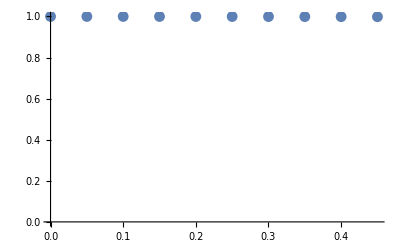

```mathematica
ListPlot[shift,PlotRange->{All,{0,1}}]
```

## tophat fractional power clipping

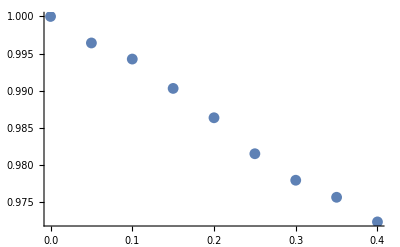

```mathematica
(*xrand, yrand are random coordinates evenly sampling incident beam of waist w (ie tophat intensity profile)*)
(*sum up the number of points that end up inside the objective aperture*)
Clear[shiftX];
R=18/2;
nn=10000;
w=R;.9R;
xrand=RandomReal[{-w,w},nn];
yrand=RandomReal[{-w,w},nn];
beamPts=Cases[Thread[{xrand,yrand}],x_/;Norm[x]<w];
n=Length[beamPts];
data=Reap[Do[
Sow[{shiftX,1/n Total[Boole[#<R^2]&/@((beamPts[[;;,1]]-shiftX)^2+beamPts[[;;,2]]^2)],Show[{
PolarPlot[R,{θ,0,2Pi}],
ListPlot[#-{shiftX,0}&/@beamPts,PlotRange->{{-R,R},{-R,R}}]
}]}];

,{shiftX,0,0.4,.05}]][[2,1]];
ListPlot[data[[;;,{1,2}]]]
```

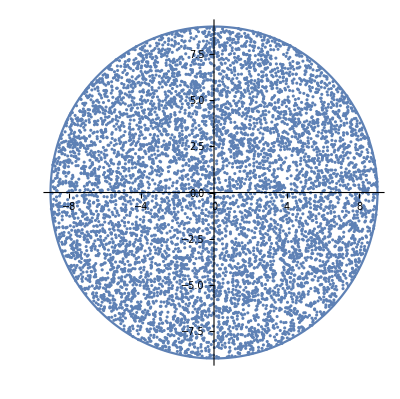
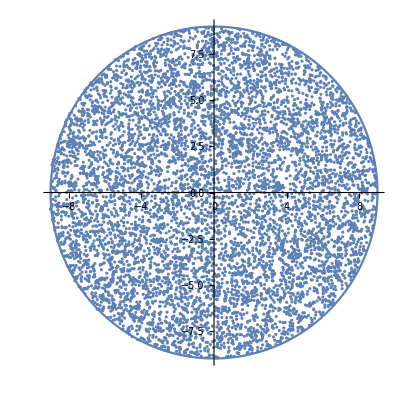
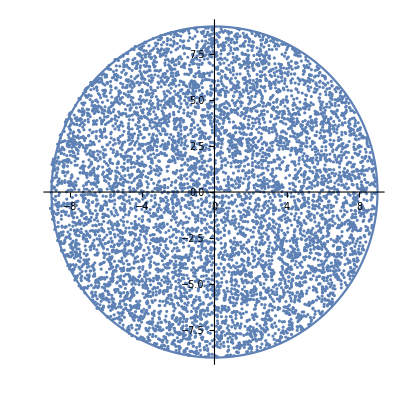
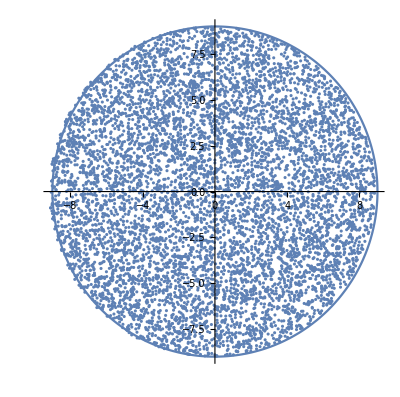
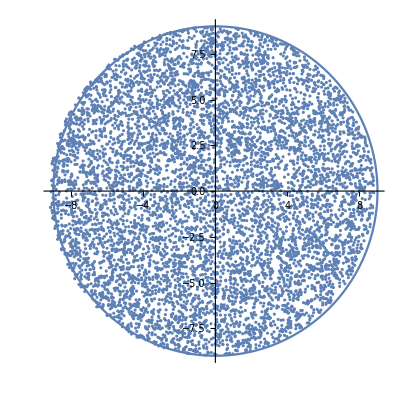
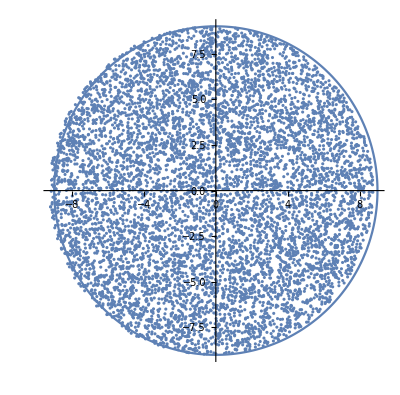
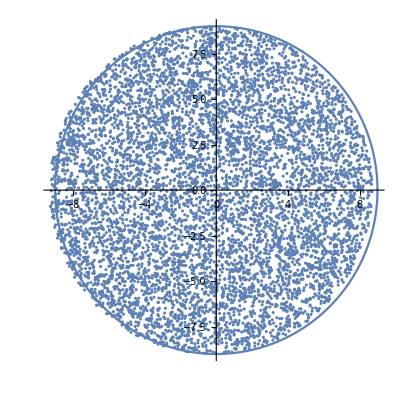
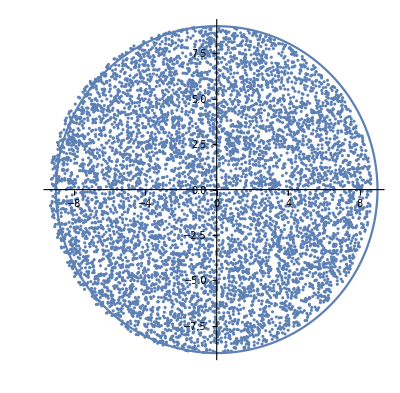

```mathematica
Partition[data[[;;,3]],3]
```